```mathematica
EdgeNum[1->4]
```

3

```mathematica
EdgeNumList[{3->8,4->1,8->9,1->2,9->3,2->4,3->1,4->9,8->2}]
```

{22,3,43,1,23,11,2,29,15}

```mathematica
Ruleg[[{22,3,43,1,23,11,2,29,15}]]
```

{3→8,1→4,8→9,1→2,3→9,2→4,1→3,4→9,2→8}

```mathematica
{3->9,9->1,1->7,7->8,8->2,2->5,5->3}
```

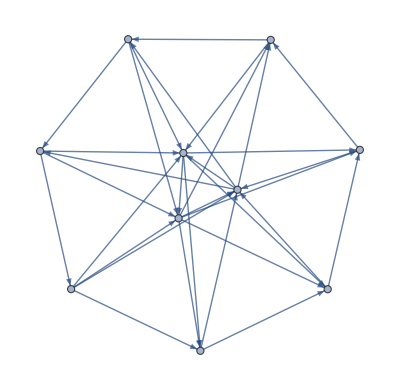

```mathematica
Gout=EdgeDelete[Gout,EdgeRules[Gout][[EdgeNumList[{8->4,2->3,4->9,3->1,9->7,1->8,7->2,8->3,2->9,4->1,3->7,9->8,1->2,7->4}]]]]
```

```mathematica
Ruleg=EdgeRules[Gin]
```

{1→5,1→6,1→7,1→9,1→10,2→4,2→5,2→6,2→8,2→10,3→4,3→5,3→6,3→9,3→10,4→5,4→6,4→10,5→6,5→7,5→8,5→9,5→10,6→7,6→8,6→9,6→10,7→8,7→10,8→10,9→10}

```mathematica
{8->2,2->4,4->3,3->9,9->1,1->7,7->8}
```

```mathematica
Curr/PD
```

{0.00704853,-0.0505656,0.457662,-0.436717,0.0972312,0.220276,0.0646117,0.136933,-1.25435,-0.0965215,-0.345826,-0.0866106,0.170834,0.977767,-0.092501,-0.0564632,0.0908992,-0.140888,0.0609338,-0.00894465,-0.0651797,0.0645645,-0.275719,0.271513,0.185387,-0.10418,0.0887364,0.30442,0.156889,0.0605435,0.0247403}

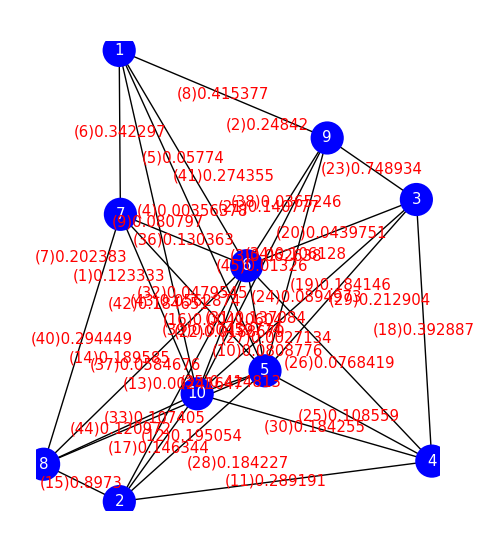

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[(Curr/PD)[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値*距離の幾何学表示 *)
```

```mathematica
MaxPartLoop={};
For[i=3,Length[MaxPartLoop]==0,i++,
MaxPartLoop=FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[Range[i]]]]]],
Infinity,All];
]
MaxPartLoop=EdgeRules[MaxPartLoop[[1]]]
```

{4→3,3→9,9→1,1→7,7→8,8→2,2→4}

```mathematica
i
```

8

```mathematica
Curr=Delete[Curr,Table[{i},{i,EdgeNumList[{8->4,2->3,4->9,3->1,9->7,1->8,7->2,8->3,2->9,4->1,3->7,9->8,1->2,7->4}]}]]
```

{-0.0240012,-0.276503,1.07221,-1.80092,0.543911,1.75208,0.732265,0.0123955,-1.45483,0.372679,-1.96784,-0.8067,0.153961,1.55723,-0.502725,-0.395424,0.39655,-0.864464,0.279612,-0.19584,-0.495815,0.489022,-0.57084,0.341288,0.318267,-0.105613,0.0120739,1.4721,0.689593,0.392588,-0.0728152}

```mathematica
DelEleList[FindCycle[
Graph[EdgeList[Gout][[Reverse[Ordering[Abs[Curr]]][[1;;10]]]]],
Infinity,All],{{4->3,3->9,9->1,1->7,7->8,8->2,2->4}}]
```

{{3->9,9->1,1->7,7->8,8->2,2->5,5->3}}

```mathematica
Curr
```

{1.06346,-1.58627,-0.619287,-0.0240012,-0.276503,1.07221,1.62741,-1.80092,0.543911,0.656841,1.75208,0.732265,0.0123955,-1.04089,-1.45483,0.0329175,0.372679,-1.96784,-0.8067,0.153961,0.802182,-0.165538,1.55723,-0.502725,-0.395424,0.39655,0.0206839,-1.37525,1.38286,-0.864464,0.279612,-0.19584,-0.495815,0.489022,-0.57084,0.341288,0.318267,-0.105613,0.0120739,1.4721,-1.16206,0.689593,-0.466253,0.392588,-0.0728152}

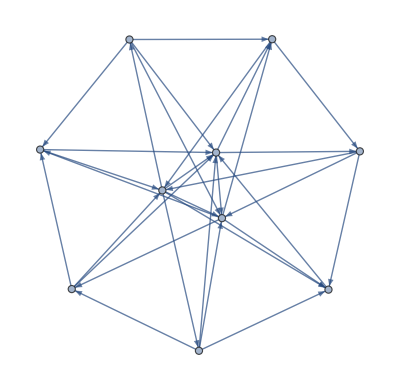

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]](* 電流値の正負をグラフの向きに反映した出力グラフ *)
```